# SEMINARSKA NALOGA

## RAČUNALNIŠKA ORODJA V MATEMATIKI

AJLA SOVIĆ

## PROSTI PAD

Prosti pad je enakomerno pospešeno gibanje navpično navzdol, brez lastnega pogona v težnostnem polju, pri katerem na telo deluje sila teže. Pospešek pri prostem padu imenujemo težni pospešek in ga označujemo z g.

```mathematica
g:=9.81m/s^2
```

Pri prostem padu imamo enake enačbe kot pri enakomernem pospešnem gibanju, le da pospešek (a) nadomestimo z g. Pri prostem padu ima telo v začetku hitrost 0, in mu nato narašča s težnim pospeškom g.

```mathematica
v= g * t      
s= g * t^2/2
```

(49.5227 m)/(√(s^2))

125. m

## NALOGA I

Telo spustimo iz višine 125 m tako, da prosto pada proti tlom. Koliko časa bo padalo?

```mathematica
h= 125m
g = 9.81 m/s^2
```

125 m

(9.81 m)/s^2

```mathematica
t = Sqrt[(2*h)/g]
```

0.451524 √((h s^2)/m)

```mathematica
4.38192376090716 √m
```

4.38192 √m

## NALOGA II

Kamen spustimo z vrha stolpnice, da prosto pade. Za pot od 8.nadstropja na višini 24m, do 7.nadstropja na višini 21m,porabi kamen čas 0.08s. S kolikšne višine smo kamen spustili?

```mathematica
h1 = 24m
h2 = 21m
g = 9.81m/s^2
t = 0.08 s
```

24 m

21 m

(9.81 m)/s^2

0.08 s

Odvisnost poti kamna od 8. do 7. nadstropja od časa zapišemo pomočjo ene izmed osnovnih fizikalnih formul

```mathematica
h1-h2= v*t + (g*t^2)/2
Solve[h1 - h2 = t * Sqrt[2*g(h-h1)] + (g*t^2)/2,h]
```

0.094176 m

Solve[0.031392 m+2.96861 √(m^2/s^2) s,94.1822 m]

## NALOGA III

Če učbenik fizike izpustimo z največjega drevesa a svetu, bo potreboval 5 sekund da pade na tla. Kolikšna je dolžina poti, ki jo je prepotoval?

```mathematica
t=5
g = 9.81
d= 1/2*(-g)*t^2
```

5

9.81

```mathematica
d
```

-490.5

Ko vidite, da učbenik fizike ni bil poškodovan, se odločite, da boste šli na streho stavbe nebotičnika in svojo knjigo spet spustili, tokrat traja 10s. Kolikšna je zdaj dolžina poti, glede na to da je knjiga padla za dvokratno količino časa?

```mathematica
t= 10
g = 9.81
d=1/2(-g)*t^2
```

10

9.81

-490.5

```mathematica
idealniPodatki = Table[{i,0.5*9.81i^2},{i,5,10,1}];
Prepend[idealniPodatki,{"čas","dolžinaPoti"}]
```

{{čas,dolžinaPoti},{5,122.625},{6,176.58},{7,240.345},{8,313.92},{9,397.305},{10,490.5}}

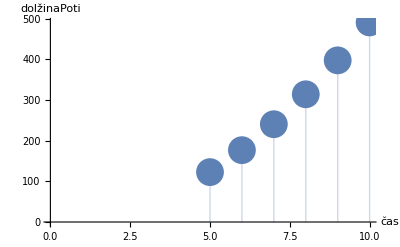

```mathematica
Show[ListPlot[idealniPodatki,AxesOrigin->{0,0},AxesLabel->{"čas","dolžinaPoti"},Filling->Axis,PlotStyle->PointSize[0.05]]]
```

Zgornji graf predstavlja graf dolžine poti v odvisnosti od časa.

## NEENAKOMERNO GIBANJE

Kadar se telesu pri gibanju spreminja hitrost, se telo giblje neenakomerno. Če se telesu hitrost povečuje, se telo giblje pospešno. Primer pospešnega gibanja je speljevanje avtomobila z mesta. Pospešno gibanje opišemo s pospeškom, za koliko se je telesu spremenila hitrost v določenem času.

## NALOGA I

Ana se je s konstantno hitrostjo 80km/h z avtomobilom vozila proti Zagrebu. Po 20 km ji je zmanjkalo goriva, zato je šla 2km peš do najbližje črpalke. Do črpalke je potrebovala pol ure. Poiščite graf poti v odvisnosti od časa.Osnovne formule v fiziki katere bomo rabili pri naslednji nalogi so:

```mathematica
ClearAll[v, s, t]
v= s/t
s=v*t
t= s/v
```

s/t

s

t

```mathematica
t2 = 0.5
v1 = 80
s1=20
s2=2
```

0.5

80

20

2

Glede na to da imamo dve poti, rabimo dve hitrosti in dva časa.

```mathematica
v2 = s2/t2
```

4.

```mathematica
t1=s1/v1
```

1/4

Ana se 20 km peljala z hitrostjo 80 km/h, in to je 1/4 ure, oziroma 0.25 h.

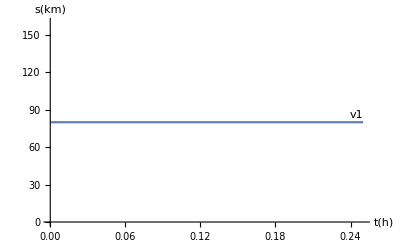

```mathematica
ClearAll[t,h]
Slika1  =Plot[v1 = s1/t1,{v,0,t1},AxesLabel->{t[h],s[km]},PlotLabels->Placed["v1",Above]]
```

Potem je 2 km šla peš, z hitrostjo 4km/h, in to je trajal pol ure.

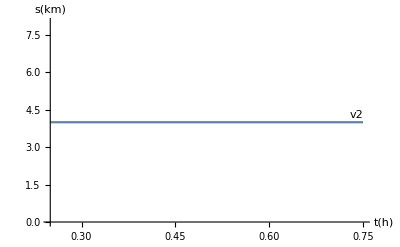

```mathematica
ClearAll[t,h]
Slika2 = Plot[v2 = s2/t2,{v,t1,t1+t2},AxesLabel->{t[h],s[km]},PlotLabels->Placed["v2",Above]]
```

## TERMODINAMIKA

Temperatura je fizikalna veličina, ki se izraža s toplotnim stanjem nekega telesa in je ena od osnovnih veličin v termodinamiki. V naslednjem primeru si bomo ogledali funkcijo dolžine v odvisnosti od temperature.

## NALOGA I

Palice iz različnih materialov pri temperaturi 0 C merijo 1 m. Dolžina se glede na temperaturo spreminja. Bomo najprej predstavili formulo za dolžino v odvisnosti od temperature.

```mathematica
L:= L0(1+A*T)                  (*L0 -> dolžina pri 0 .baC, A->  temperaturni koeficient linearnega raztezka, T -> temperatura v 0 .baC*)
```

Temperaturni koeficienti linearnega raztezka so naslednji: 
Jeklo → 6,7 * 10(-6) .baC;
 Baker  → 16,6 * 10(-6) .baC;
 Aluminij → 25,0 * 10(-6) .baC.
 Predstavimo graf dolžine v odvisnosti od temperature.

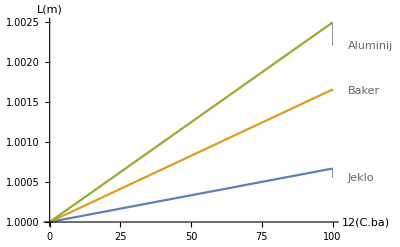

```mathematica
ClearAll[L,m]
Plot[{1*(1+6.7*10^(-6)*T),1*(1+16.6*10^(-6)*T),1*(1+25.0*10^(-6)*T)},{T,0,100},PlotLabels->{"Jeklo","Baker","Aluminij"},AxesLabel->{T[C.ba],L[m]}]
```